# Mushrooms - Edible or Poisonous?

```mathematica
Hyperlink["http://archive.ics.uci.edu/ml/datasets/Mushroom"]
```

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/mushroom/agaricus-lepiota.data","CSV"];
```

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All]&
```

p | x | s | w | t | p | f | c | n | k | e | e | s | s | w | w | p | w | o | p | n | s | u
p | f | y | y | f | f | f | c | b | g | e | b | k | k | p | p | p | w | o | l | h | y | p
p | f | f | y | f | f | f | c | b | p | e | b | k | k | b | n | p | w | o | l | h | y | g
e | x | y | e | t | n | f | c | b | p | t | b | s | s | p | g | p | w | o | p | k | y | d
p | x | y | y | f | f | f | c | b | g | e | b | k | k | b | n | p | w | o | l | h | v | g
e | x | y | e | t | n | f | c | b | u | t | b | s | s | p | g | p | w | o | p | k | y | d
p | x | s | b | t | f | f | c | b | w | t | b | s | f | w | w | p | w | o | p | h | s | g
e | b | y | n | f | n | f | c | b | w | e | b | y | y | n | n | p | w | t | p | w | y | p
p | f | s | g | t | f | f | c | b | p | t | b | s | s | w | w | p | w | o | p | h | s | g
p | f | s | b | t | f | f | c | b | h | t | b | f | f | w | w | p | w | o | p | h | s | u

```mathematica
Take[rawdata,1]
```

{{p,x,s,n,t,p,f,c,n,k,e,e,s,s,w,w,p,w,o,p,k,s,u}}

```mathematica
labelEncoding=ImportString[
"1. cap-shape:                bell=b,conical=c,convex=x,flat=f,knobbed=k,sunken=s
     2. cap-surface:              fibrous=f,grooves=g,scaly=y,smooth=s
     3. cap-color:                brown=n,buff=b,cinnamon=c,gray=g,green=r,pink=p,purple=u,red=e,white=w,yellow=y
     4. bruises?:                 bruises=t,no=f
     5. odor:                     almond=a,anise=l,creosote=c,fishy=y,foul=f,musty=m,none=n,pungent=p,spicy=s
     6. gill-attachment:          attached=a,descending=d,free=f,notched=n
     7. gill-spacing:             close=c,crowded=w,distant=d
     8. gill-size:                broad=b,narrow=n
     9. gill-color:               black=k,brown=n,buff=b,chocolate=h,gray=g,green=r,orange=o,pink=p,purple=u,red=e,white=w,yellow=y
    10. stalk-shape:              enlarging=e,tapering=t
    11. stalk-root:               bulbous=b,club=c,cup=u,equal=e,rhizomorphs=z,rooted=r,missing=?
    12. stalk-surface-above-ring: fibrous=f,scaly=y,silky=k,smooth=s
    13. stalk-surface-below-ring: fibrous=f,scaly=y,silky=k,smooth=s
    14. stalk-color-above-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    15. stalk-color-below-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    16. veil-type:                partial=p,universal=u
    17. veil-color:               brown=n,orange=o,white=w,yellow=y
    18. ring-number:              none=n,one=o,two=t
    19. ring-type:                cobwebby=c,evanescent=e,flaring=f,large=l,none=n,pendant=p,sheathing=s,zone=z
    20. spore-print-color:        black=k,brown=n,buff=b,chocolate=h,green=r,orange=o,purple=u,white=w,yellow=y
    21. population:               abundant=a,clustered=c,numerous=n,scattered=s,several=v,solitary=y
    22. habitat:                  grasses=g,leaves=l,meadows=m,paths=p,urban=u,waste=w,woods=d","Lines"];
```

```mathematica
labelEncoding[[3]]
```

3. cap-color:                brown=n,buff=b,cinnamon=c,gray=g,green=r,pink=p,purple=u,red=e,white=w,yellow=y

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
rules=Join[
{{"e"->"edible","p"->"poisonous"}},
Map[
StringCases[#,(a:LetterCharacter..)~~"="~~(b:LetterCharacter|"?"):>(b->a)]&,
labelEncoding
]];
```

```mathematica
Length[rules]
```

23

```mathematica
rules[[2]]
```

{b→bell,c→conical,x→convex,f→flat,k→knobbed,s→sunken}

```mathematica
rules[[3]]
```

{f→fibrous,g→grooves,y→scaly,s→smooth}

```mathematica
rules[[23]]
```

{g→grasses,l→leaves,m→meadows,p→paths,u→urban,w→waste,d→woods}

```mathematica
Length[rawdata]
```

8124

```mathematica
rawdata[[1]]
```

{p,x,s,n,t,p,f,c,n,k,e,e,s,s,w,w,p,w,o,p,k,s,u}

```mathematica
rawdataTransposed=Transpose[rawdata];
```

```mathematica
Take[rawdataTransposed[[1]],10]/.rules[[1]]
```

{poisonous,edible,edible,poisonous,edible,edible,edible,edible,poisonous,edible}

```mathematica
MapThread[f,{{1,2,3},{a,b,c}}]
```

{f[1,a],f[2,b],f[3,c]}

```mathematica
Length[rawdataTransposed]
```

23

```mathematica
Length[rules]
```

23

```mathematica
rawdataProcessed=MapThread[#1/.#2&,{rawdataTransposed,rules}];
```

```mathematica
rawdataLabeled=Transpose[rawdataProcessed];
```

```mathematica
RandomSample[rawdataLabeled,5]
```

{{edible,convex,smooth,white,no,none,free,crowded,broad,black,tapering,equal,smooth,smooth,white,white,partial,white,one,evanescent,black,abundant,grasses},{poisonous,convex,fibrous,gray,no,foul,free,close,broad,chocolate,enlarging,bulbous,silky,silky,brown,pink,partial,white,one,large,chocolate,solitary,woods},{edible,flat,scaly,red,bruises,none,free,close,broad,white,tapering,bulbous,smooth,smooth,pink,pink,partial,white,one,pendant,black,several,woods},{edible,knobbed,smooth,gray,no,none,free,crowded,broad,white,enlarging,missing,silky,smooth,white,white,partial,white,two,pendant,white,scattered,grasses},{poisonous,convex,fibrous,gray,no,foul,free,close,broad,chocolate,enlarging,bulbous,silky,silky,buff,pink,partial,white,one,large,chocolate,solitary,woods}}

```mathematica
Length[rawdataLabeled]
```

8124

```mathematica
{rawdata1,rawdata2}=Partition[RandomSample[rawdataLabeled],5000,5000,1,{}];
```

```mathematica
Length[rawdata2]
```

3124

```mathematica
rawdata1[[1]]
```

{poisonous,knobbed,scaly,brown,no,fishy,free,close,narrow,buff,tapering,missing,smooth,smooth,white,white,partial,white,one,evanescent,white,several,leaves}

```mathematica
keys={"result","cap-shape","cap-surface","cap-color","bruises","odor","gill-attachment","gill-spacing","gill-size","gill-color","stalk-shape","stalk-root","stalk-surface-above-ring","stalk-surface-below-ring","stalk-color-above-ring","stalk-color-below-ring","veil-type","veil-color","ring-number","ring-type","spore-print-color","population","habitat"};
```

```mathematica
Length[keys]
```

23

```mathematica
AssociationThread[keys->rawdata1[[1]]]
```

<|result→poisonous,cap-shape→knobbed,cap-surface→scaly,cap-color→brown,bruises→no,odor→fishy,gill-attachment→free,gill-spacing→close,gill-size→narrow,gill-color→buff,stalk-shape→tapering,stalk-root→missing,stalk-surface-above-ring→smooth,stalk-surface-below-ring→smooth,stalk-color-above-ring→white,stalk-color-below-ring→white,veil-type→partial,veil-color→white,ring-number→one,ring-type→evanescent,spore-print-color→white,population→several,habitat→leaves|>

```mathematica
keys//Length
```

23

```mathematica
rawdata[[1]]//Length
```

23

```mathematica
training=Dataset[
Map[AssociationThread[keys->#]&,rawdata1]
]
```

Dataset[<>]

```mathematica
{1,2,3,4,5}[[2;;-1]]
```

{2,3,4,5}

```mathematica
Union[{1,1,2,2,3,3}]
```

{1,2,3}

```mathematica
allLabels=Map[Union,Transpose[rawdataLabeled][[2;;-1]]]
```

{{bell,conical,convex,flat,knobbed,sunken},{fibrous,grooves,scaly,smooth},{brown,buff,cinnamon,gray,green,pink,purple,red,white,yellow},{bruises,no},{almond,anise,creosote,fishy,foul,musty,none,pungent,spicy},{attached,free},{close,crowded},{broad,narrow},{black,brown,buff,chocolate,gray,green,orange,pink,purple,red,white,yellow},{enlarging,tapering},{bulbous,club,equal,missing,rooted},{fibrous,scaly,silky,smooth},{fibrous,scaly,silky,smooth},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{partial},{brown,orange,white,yellow},{none,one,two},{evanescent,flaring,large,none,pendant},{black,brown,buff,chocolate,green,orange,purple,white,yellow},{abundant,clustered,numerous,scattered,several,solitary},{grasses,leaves,meadows,paths,urban,waste,woods}}

```mathematica
encoders=Table[
NetEncoder[{"Class",label,"UnitVector"}],
{label,allLabels}];
```

```mathematica
encoders[[1]]["sunken"]
```

{0,0,0,0,0,1}

```mathematica
Manipulate[
Grid[Map[{#,encoders[[a]][#]}&,allLabels[[a]]],Frame->All],
{a,1,22,1}]
```

Part::partd: Part specification allLabels⟦22⟧ is longer than depth of object.

Part::partd: Part specification encoders⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {22,encoders⟦22⟧[22]} cannot be used as a part specification.

Part::partd: Part specification encoders⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification encoders⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
netports=Rest[NetPort/@keys]
```

{NetPort[cap-shape],NetPort[cap-surface],NetPort[cap-color],NetPort[bruises],NetPort[odor],NetPort[gill-attachment],NetPort[gill-spacing],NetPort[gill-size],NetPort[gill-color],NetPort[stalk-shape],NetPort[stalk-root],NetPort[stalk-surface-above-ring],NetPort[stalk-surface-below-ring],NetPort[stalk-color-above-ring],NetPort[stalk-color-below-ring],NetPort[veil-type],NetPort[veil-color],NetPort[ring-number],NetPort[ring-type],NetPort[spore-print-color],NetPort[population],NetPort[habitat]}

```mathematica
Rest[{1,2,3}]
```

{2,3}

```mathematica
port2encoders=MapThread[Rule,{Rest[keys],encoders}];
```

```mathematica
port2encoders[[1]]
```

cap-shape→None

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[80],
ElementwiseLayer[Tanh],
DotPlusLayer[2],
SoftmaxLayer[]
},{
netports->1,1->2,2->3,3->4,4->5,5->NetPort["result"]
},
Sequence@@port2encoders,
"result"->NetDecoder[{"Class",{"edible","poisonous"}}]
]
```

NetGraph[]

```mathematica
net=NetInitialize[net];
```

```mathematica
result=NetTrain[net,Take[training,1000],MaxTrainingRounds->20]
```

NetGraph[]

```mathematica
rawdata2
```

```mathematica
validation=Table[r[[2;;-1]]->r[[1]],{r,rawdata2}];
```

```mathematica
RandomSample[validation,10]//Column
```

{bell,smooth,brown,no,none,attached,close,broad,brown,enlarging,missing,smooth,smooth,orange,orange,partial,orange,one,pendant,brown,clustered,leaves}→edible
{convex,smooth,white,bruises,foul,free,close,broad,chocolate,tapering,bulbous,smooth,fibrous,white,white,partial,white,one,pendant,chocolate,several,grasses}→poisonous
{flat,fibrous,gray,no,foul,free,close,broad,chocolate,enlarging,bulbous,silky,silky,pink,buff,partial,white,one,large,chocolate,solitary,woods}→poisonous
{convex,smooth,brown,no,none,attached,close,broad,orange,enlarging,missing,smooth,smooth,orange,orange,partial,orange,one,pendant,orange,several,leaves}→edible
{flat,scaly,red,no,fishy,free,close,narrow,buff,tapering,missing,smooth,smooth,white,pink,partial,white,one,evanescent,white,several,paths}→poisonous
{convex,fibrous,brown,bruises,none,free,close,broad,brown,tapering,bulbous,smooth,smooth,white,gray,partial,white,one,pendant,brown,solitary,woods}→edible
{convex,smooth,red,no,spicy,free,close,narrow,buff,tapering,missing,silky,smooth,white,pink,partial,white,one,evanescent,white,several,paths}→poisonous
{convex,fibrous,yellow,no,foul,free,close,broad,pink,enlarging,bulbous,silky,silky,pink,brown,partial,white,one,large,chocolate,solitary,paths}→poisonous
{convex,smooth,brown,no,none,free,crowded,broad,chocolate,tapering,equal,smooth,smooth,white,white,partial,white,one,evanescent,brown,scattered,grasses}→edible
{knobbed,scaly,brown,bruises,none,free,close,broad,red,enlarging,missing,smooth,smooth,red,red,partial,white,two,evanescent,white,clustered,waste}→edible

```mathematica
{"convex","fibrous","yellow","no","foul","free","close","broad","pink","enlarging","bulbous","silky","silky","pink","brown","partial","white","one","large","chocolate","solitary","paths"}->"poisonous"
```

```mathematica
aaa=AssociationThread[Rest[keys]->{"convex","fibrous","yellow","no","foul","free","close","broad","pink","enlarging","bulbous","silky","silky","pink","brown","partial","white","one","large","chocolate","solitary","paths"}]
```

<|cap-shape→convex,cap-surface→fibrous,cap-color→yellow,bruises→no,odor→foul,gill-attachment→free,gill-spacing→close,gill-size→broad,gill-color→pink,stalk-shape→enlarging,stalk-root→bulbous,stalk-surface-above-ring→silky,stalk-surface-below-ring→silky,stalk-color-above-ring→pink,stalk-color-below-ring→brown,veil-type→partial,veil-color→white,ring-number→one,ring-type→large,spore-print-color→chocolate,population→solitary,habitat→paths|>

```mathematica
result[<|"cap-shape"->"convex","cap-surface"->"fibrous","cap-color"->"yellow","bruises"->"no","odor"->"foul","gill-attachment"->"free","gill-spacing"->"close","gill-size"->"broad","gill-color"->"pink","stalk-shape"->"enlarging","stalk-root"->"bulbous","stalk-surface-above-ring"->"silky","stalk-surface-below-ring"->"silky","stalk-color-above-ring"->"pink","stalk-color-below-ring"->"brown","veil-type"->"partial","veil-color"->"white","ring-number"->"one","ring-type"->"large","spore-print-color"->"chocolate","population"->"solitary","habitat"->"paths"|>]
```

poisonous

```mathematica
result[<|"cap-shape"->"convex","cap-surface"->"fibrous","cap-color"->"yellow","bruises"->"no","odor"->"foul","gill-attachment"->"free","gill-spacing"->"close","gill-size"->"broad","gill-color"->"pink","stalk-shape"->"enlarging","stalk-root"->"bulbous","stalk-surface-above-ring"->"silky","stalk-surface-below-ring"->"silky","stalk-color-above-ring"->"pink","stalk-color-below-ring"->"brown","veil-type"->"partial","veil-color"->"white","ring-number"->"one","ring-type"->"large","spore-print-color"->"chocolate","population"->"solitary","habitat"->"paths"|>,"Probabilities"]
```

<|edible→0.000264374,poisonous→0.999736|>

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

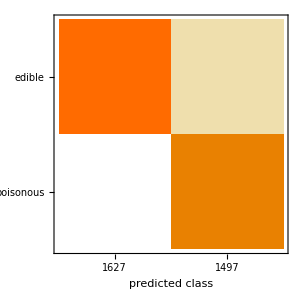

```mathematica
cm["ConfusionMatrixPlot"]
```